## SphericalHarmonics

```mathematica
Yc[m_,l_,x_,y_,z_]:=(1-z^2)^(m/2)ChebyshevT[m,x/Sqrt[1-z^2]] JacobiP[l-m,m,m,z];
Yc[m_,l_,θ_,φ_]:=Sin[φ]^m Cos[m θ]JacobiP[l-m,m,m,Cos[φ]];
Ys[m_,l_,x_,y_,z_]:=(1-z^2)^((m-1)/2)y ChebyshevU[m-1,x/Sqrt[1-z^2]] JacobiP[l-m,m,m,z];
Ys[m_,l_,θ_,φ_]:=Sin[φ]^m Sin[m θ]JacobiP[l-m,m,m,Cos[φ]];
SphereIntegrate[f_,{x_,y_,z_}]:=Module[{φ,θ,ex},
ex=f /.{x->Sin[φ]Cos[θ],y->Sin[φ]Sin[θ],z->Cos[φ]};
∫_0^π ∫_0^(2π) ex Sin[φ]ⅆθⅆφ
];
SphereNIntegrate[f_,{x_,y_,z_}]:=Module[{φ,θ,ex},
ex=f /.{x->Sin[φ]Cos[θ],y->Sin[φ]Sin[θ],z->Cos[φ]};
NIntegrate[ex Sin[φ],{φ,0,π},{θ,-π,π}]
];
DiskIntegrate[f_,{x_,y_}]:= ∫_-1^1 ∫_(-Sqrt[1-x^2])^Sqrt[1-x^2] fⅆyⅆx
```

```mathematica
Clear[x,y,z]
```

```mathematica
SGrad[f_,{x_,y_,z_}]:=Grad[f,{x,y,z}]-{x,y,z} ({x,y,z}.Grad[f,{x,y,z}]);
GradYc[m_,l_,x_,y_,z_]:=SGrad[Yc[m,l,x,y,z],{x,y,z}];
GradYs[m_,l_,x_,y_,z_]:=SGrad[Ys[m,l,x,y,z],{x,y,z}];
PertGradYc[m_,l_,x_,y_,z_]:=Cross[SGrad[Yc[m,l,x,y,z],{x,y,z}],{x,y,z}];
PertGradYs[m_,l_,x_,y_,z_]:=Cross[SGrad[Ys[m,l,x,y,z],{x,y,z}],{x,y,z}];
```

```mathematica
Clear[a,b,c];
a[x_,y_,z_]:={y,-x,0};
b[x_,y_,z_]:={z,0,-x};
c[x_,y_,z_]:= {0,z,-y};
```

```mathematica
eφ[θ_,φ_]:={Cos[θ]Cos[φ],Sin[θ]Cos[φ],-Sin[φ]};
eθ[θ_,φ_]:={-Sin[θ],Cos[θ],0};
er[x_,y_,z_]:={x,y,z};
eφ[x_,y_,z_]:={x z,y z,z^2-1}/Sqrt[1-z^2];
eθ[x_,y_,z_]:=-a[x,y,z]/Sqrt[1-z^2];
```

## Relationship between a,b,c and eθ,eφ

```mathematica
a[x,y,z]==-Sqrt[1-z^2] eθ[x,y,z]//Simplify
```

True

```mathematica
b[x,y,z]==x/Sqrt[1-z^2] eφ[x,y,z]-(y z)/Sqrt[1-z^2] eθ[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
c[x,y,z]==y/Sqrt[1-z^2] eφ[x,y,z]+(x z)/Sqrt[1-z^2] eθ[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
eθ[x,y,z]==(-a[x,y,z])/Sqrt[1-z^2]//Simplify
```

True

```mathematica
eφ[x,y,z]== (x b[x,y,z]+y c[x,y,z])/Sqrt[1-z^2]/.z^2->1-x^2-y^2//Simplify
```

True

## Derivation

### grads

```mathematica
df/dφ φh+1/Sin[φ] df/dθ θh
```

```mathematica
df/dφ φh+1/Sin[φ] df/dθ θh
```

```mathematica
Cos[φ]==z
```

```mathematica
Sin[φ]==Sqrt[x^2+y^2]
```

```mathematica
x==Cos[θ] Sin[φ];
y==Sin[θ]Sin[φ]
```

```mathematica
dx==Cos[θ]Cos[φ]dφ
dx/dφ==Cos[θ]Cos[φ]==(z x)/Sqrt[1-z^2]
dy/dφ==Sin[θ]Cos[φ]==(z y)/Sqrt[1-z^2]
```

```mathematica
-Sin[φ] dφ == dz
```

```mathematica
df/dφ==df/dz dz/dφ+df/dx dx/dφ+df/dy dy/dφ==-Sin[φ] df/dz+df/dx dx/dφ+df/dy dy/dφ==-Sqrt[1-z^2] df/dz+(z x)/Sqrt[1-z^2] df/dx+(z y)/Sqrt[1-z^2] df/dy=={(z x)/Sqrt[1-z^2],(z y)/Sqrt[1-z^2],-Sqrt[1-z^2]}Grad[f,{x,y,z}]==
φh Grad[f,{x,y,z}]
```

```mathematica
dx==-Sin[θ]Sin[φ]dθ==-y dθ
dy==Cos[θ]Sin[φ]dθ==x dθ
```

```mathematica
df/dθ==df/dx
```

```mathematica
df/dφ φh+1/Sin[φ] df/dθ θh
```

### grad Sphers

```mathematica
df/dφ φh+1/Sin[φ] df/dθ θh
```

```mathematica
(d/dφ)[Cos[m θ] Sin[φ]^m JacobiP[l-m,m,m,Cos[φ]]]==
-Cos[m θ]Sqrt[1-z^2](d/dz)[(1-z^2)^(m/2) JacobiP[l-m,m,m,z]]==
-Cos[m θ]((1-z^2)^((m-1)/2))[-m z+(1-z^2)d/dz] JacobiP[l-m,m,m,z]==
-Cos[m θ]((1-z^2)^((m-1)/2))[-2 m z+(1-z^2)d/dz] JacobiP[l-m,m,m,z]+Cos[m θ](1-z^2)^((m-1)/2)m z  JacobiP[l-m,m,m,z]
```

## Grad defs

```mathematica
φh[x_,y_,z_]:={(z x)/Sqrt[1-z^2],(z y)/Sqrt[1-z^2],-Sqrt[1-z^2]};
θh[x_,y_,z_]:={-y,x,0}/Sqrt[1-z^2];
Dφ[f_,{x_,y_,z_}]:=φh[x,y,z].Grad[f,{x,y,z}];
Dθ[f_,{x_,y_,z_}]:=Sqrt[1-z^2]θh[x,y,z] . Grad[f,{x,y,z}];
```

```mathematica
SGrad2[f_,{x_,y_,z_}]:=Dφ[f,{x,y,z}] φh[x,y,z]+1/Sqrt[1-z^2] Dθ[f,{x,y,z}] θh[x,y,z]
```

```mathematica
SGrad[f[x,y,z],{x,y,z}]//ExpandAll
```

{-x z f^(0,0,1)[x,y,z]-x y f^(0,1,0)[x,y,z]+f^(1,0,0)[x,y,z]-x^2 f^(1,0,0)[x,y,z],-y z f^(0,0,1)[x,y,z]+f^(0,1,0)[x,y,z]-y^2 f^(0,1,0)[x,y,z]-x y f^(1,0,0)[x,y,z],f^(0,0,1)[x,y,z]-z^2 f^(0,0,1)[x,y,z]-y z f^(0,1,0)[x,y,z]-x z f^(1,0,0)[x,y,z]}

```mathematica
SGrad2[Ys[2,2,x,y,z],{x,y,z}]/.z^2->1-x^2-y^2//Simplify
```

{(2-4 x^2) y,x (2-4 y^2),-4 x y z}

```mathematica
SGrad[Ys[2,2,x,y,z],{x,y,z}]//Simplify
```

{(2-4 x^2) y,x (2-4 y^2),-4 x y z}

```mathematica
{(1-x^2(1-z^2)-z^2)/(1-z^2),-x y,-x z} //Simplify
```

{1-x^2,-x y,-x z}

```mathematica
{(y^2+x^2 (1-x^2-y^2))/(x^2+y^2),-x y,-x z}
```

```mathematica
{(y^2+x^2 -x^4-x^2 y^2)/(x^2+y^2),-x y,-x z}
```

```mathematica
SGrad[Yc[1,1,x,y,z],{x,y,z}]
```

{1-x^2,-x y,-x z}

```mathematica
SGrad[Yc[0,1,x,y,z],{x,y,z}]
```

{-x z,-y z,1-z^2}

```mathematica
SGrad[Ys[1,1,x,y,z],{x,y,z}]
```

{-x y,1-y^2,-y z}

## relation with phi and θ

```mathematica
(a=Curl[SGrad[Yc[0,1,x,y,z],{x,y,z}]//Simplify,{x,y,z}])//MatrixForm
```

(y
-x
0)

```mathematica
(b=Curl[SGrad[Yc[1,1,x,y,z],{x,y,z}]//Simplify,{x,y,z}])//MatrixForm
```

(0
z
-y)

```mathematica
(c=Curl[SGrad[Ys[1,1,x,y,z],{x,y,z}]//Simplify,{x,y,z}])//MatrixForm
```

(-z
0
x)

```mathematica
z a +y c + x b
```

{0,0,0}

### all others generated from a,b,c

```mathematica
SGrad[Yc[0,1,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

(-x z
-y z
1-z^2)

```mathematica
SGrad[Yc[1,1,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

(1-x^2
-x y
-x z)

```mathematica
SGrad[Ys[1,1,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

(-x y
1-y^2
-y z)

```mathematica
SGrad[Yc[0,1,x,y,z],{x,y,z}]-x c+y b/.z^2->1-x^2-y^2//Simplify//MatrixForm
```

(0
0
0)

```mathematica
SGrad[Yc[1,1,x,y,z],{x,y,z}]+z c - y a/.z^2->1-x^2-y^2//Simplify//MatrixForm
```

(0
0
0)

```mathematica
SGrad[Ys[1,1,x,y,z],{x,y,z}]-z b + x a /.z^2->1-x^2-y^2//Simplify//MatrixForm
```

(0
0
0)

```mathematica
SGrad[Yc[0,1,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

```mathematica
Yc[0,0,x,y,z]
```

1

```mathematica
SGrad[Yc[1,0,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

(0
0
0)

```mathematica
SGrad[Ys[1,1,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

(-x y
1-y^2
-y z)

```mathematica
Sqrt[1-z^2]  θh[x,y,z]
```

{-y,x,0}

```mathematica
Sqrt[1-z^2]φh[x,y,z]
```

{x z,y z,-1+z^2}

```mathematica
({{1}, {2}, {3}})
```

### higher order as Jacobi

```mathematica
Curl[SGrad[Yc[0,3,x,y,z],{x,y,z}],{x,y,z}]-(3/2 (-1+15 z^2)) a//Simplify//MatrixForm
```

(0
0
0)

```mathematica
Curl[SGrad[Yc[0,3,x,y,z],{x,y,z}],{x,y,z}]-3/4 JacobiP[2,6,6,z] a//Simplify//MatrixForm
```

(0
0
0)

```mathematica
Curl[SGrad[Yc[0,4,x,y,z],{x,y,z}],{x,y,z}]-5 z (-3+14 z^2) a //Simplify//MatrixForm
```

(0
0
0)

```mathematica
JacobiP[3,9/2,9/2,z] //Simplify
```

65/16 z (-3+14 z^2)

```mathematica
Curl[SGrad[Yc[0,4,x,y,z],{x,y,z}],{x,y,z}]- 16/13 JacobiP[3,9/2,9/2,z] a //Simplify//MatrixForm
```

(0
0
0)

```mathematica
Curl[SGrad[Yc[0,5,x,y,z],{x,y,z}],{x,y,z}]//Simplify
```

{15/8 y (1-42 z^2+105 z^4),-15/8 x (1-42 z^2+105 z^4),0}

```mathematica
m=8;JacobiP[4,m,m,z]//Simplify
```

33/8 (1-42 z^2+161 z^4)

```mathematica
323/3.
```

107.667

```mathematica
102/3.
```

34.

```mathematica
408/4//N
```

101.75

```mathematica
32
```

```mathematica
2695/27//N
```

99.8148

```mathematica
323/3//N
```

107.667

```mathematica
224/3//N
```

74.6667

```mathematica
6,9/2
```

```mathematica
12/2
```

6

```mathematica
9/2
```

9/2

```mathematica
5/65
```

1/13

```mathematica
ChebyshevU[2,z]
```

-1+4 z^2

```mathematica
m=6;JacobiP[2,m,m,z]/2//Simplify
```

-1+15 z^2

```mathematica
m=9/2;JacobiP[3,m,m,z]//Simplify
```

65/16 z (-3+14 z^2)

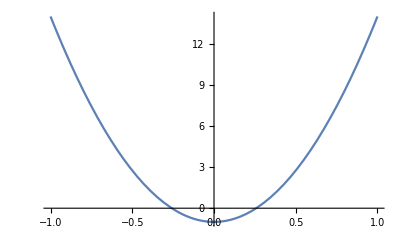

```mathematica
Plot[(-1+15 z^2),{z,-1,1}]
```

```mathematica
15  z^2+3/2  (-1+5 z^2)//Simplify
```

3/2 (-1+15 z^2)

```mathematica
//Simplify
```

{3/2 y (-1+15 z^2),-3/2 x (-1+15 z^2),0}

```mathematica
({{15  z^2+3/2  (-1+5 z^2)}, {-15 x z^2-3/2 x (-1+5 z^2)}, {0}})
```

## higher order as poly * a,b,c

### l = 1

```mathematica
PertGradYc[0,1,x,y,z]==-a[x,y,z]
```

True

```mathematica
PertGradYc[1,1,x,y,z]==-c[x,y,z]
```

True

```mathematica
PertGradYs[1,1,x,y,z]==b[x,y,z]
```

True

### l = 2

```mathematica
-PertGradYc[0,2,x,y,z]/3==z a[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[1,2,x,y,z]/-2==x a[x,y,z]+z c[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[2,2,x,y,z]/-2==z a[x,y,z]+2 x c[x,y,z]==y b[x,y,z] + x c[x,y,z]//Simplify
```

True

```mathematica
PertGradYs[1,2,x,y,z]/-2==y a[x,y,z]- z b[x,y,z]//Simplify
```

True

```mathematica
PertGradYs[2,2,x,y,z]/2==x b[x,y,z]-y c[x,y,z]//Simplify
```

True

```mathematica
-GradYc[0,1,x,y,z]==x b[x,y,z]+y c[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
GradYc[1,1,x,y,z]==y a[x,y,z]+z b[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
GradYs[1,1,x,y,z]==-x a[x,y,z]+z c[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

### l = 3

```mathematica
PertGradYc[0,3,x,y,z]==3/2(1-5 z^2)a[x,y,z]==-2JacobiP[2,1,1,z] a[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[1,3,x,y,z]==-15/2 x z a[x,y,z]-3/4 (5 z^2-1) c[x,y,z]==-15/2 x z a[x,y,z]-JacobiP[2,1,1,z] c[x,y,z]==-15/2 x y b [x,y,z]-(JacobiP[2,1,1,z] -15/2 x^2)c[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[2,3,x,y,z]/3== (1-2 x^2+z^2) a[x,y,z]-4y z b[x,y,z]==(1-2 x^2-3 z^2) a[x,y,z]-4x z c[x,y,z] //Simplify
```

True

```mathematica
PertGradYc[3,3,x,y,z]==-6 x z a[x,y,z]-3 (-1+4 x^2+z^2) c[x,y,z]//Simplify
```

True

```mathematica
PertGradYs[1,3,x,y,z]==-15/2 y z a[x,y,z] +3/4(-1+5 z^2)b[x,y,z]//Simplify
```

True

```mathematica
PertGradYs[2,3,x,y,z]==-6 y x  a[x,y,z]+6 z x b[x,y,z]-6 z y c[x,y,z]//Simplify
```

True

```mathematica
PertGradYs[3,3,x,y,z]==6 y z a[x,y,z]+(-1+4 x^2-8 y^2+z^2) b[x,y,z]//Simplify
```

True

```mathematica
GradYs[2,2,x,y,z]==(2-4 x^2) a[x,y,z]+4 x z c[x,y,z]==(2-4 x^2- 4 z^2) a[x,y,z]+4  z y b[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

#### rearrange

```mathematica
PertGradYc[0,3,x,y,z]-3/2(-1+15 z^2) a//Simplify
```

{0,0,0}

```mathematica
2/45 PertGradYc[1,3,x,y,z]-1/18 PertGradYc[3,3,x,y,z]- (2/15-2 x^2)b//Simplify
```

{0,0,0}

{0,z,-y}

```mathematica
b
```

{0,z,-y}

```mathematica
c
```

{-z,0,x}

```mathematica
a
```

{y,-x,0}

{-z (1+30 y^2-15 z^2),0,x (1+30 y^2-15 z^2)}

```mathematica
b
```

{0,z,-y}

```mathematica
a.b
```

-x z

```mathematica
a.c
```

```mathematica
a.a
```

x^2+y^2

```mathematica
a.b
```

-x z

```mathematica
a.a
```

x^2+y^2

```mathematica
b
```

{0,z,-y}

```mathematica
x a + y b + z c
```

{x y-z^2,-x^2+y z,-y^2+x z}

{0,3 z (-1+12 x^2+3 z^2),-3 y (-1+12 x^2+3 z^2)}

{0,z,-y}

{x y z,-x^2 z,0}

```mathematica
PertGradYs[1,2,x,y,z]-4 y a-4 z c//Simplify
```

{0,0,0}

```mathematica
PertGradYs[2,2,x,y,z]-4 x c-4 y b
```

{0,0,0}

### l = 4

```mathematica
PertGradYc[0,4,x,y,z]==-5/2 z (-3+7 z^2)a[x,y,z]==-5/2 JacobiP[3,1,1,z ]a[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[1,4,x,y,z]==3 x (1-7 z^2)a[x,y,z]+(3 z-7 z^3)c[x,y,z]==3 x (1-7 z^2)a[x,y,z]-JacobiP[3,1,1,z]c[x,y,z]==-3 x JacobiP[2,2,2,z]a[x,y,z]-JacobiP[3,1,1,z]c[x,y,z]//Simplify
```

True

```mathematica
(PertGradYc[2,4,x,y,z]==-4 z (-4+7 x^2+7 z^2)a[x,y,z]+ 4(1-7 z^2)x c[x,y,z]==-4 z (3-7 y^2)a[x,y,z]+ 4(1-7 z^2)x c[x,y,z] ==-4 z (3-7 y^2)a[x,y,z]- 4JacobiP[2,2,2,z]x c[x,y,z] //Simplify)/.z^2->1-x^2-y^2
```

True

### l = 5

```mathematica
PertGradYc[0,5,x,y,z]==-3 JacobiP[4,1,1,z ]a[x,y,z]//Simplify
```

```mathematica
Poly orthogonal w.r.t. Sqrt[1-x^2-z^2]
```

```mathematica
Table[DiskIntegrate[(1-x^2-z^2)^(1/2)x^k z^j JacobiP[3,2,2,z]x,{x,z}]//Print,{k,0,3},{j,0,3-k}]
```

0

0

0

«7 more identical outputs»

{{Null,Null,Null,Null},{Null,Null,Null},{Null,Null},{Null}}

```mathematica
PertGradYc[1,5,x,y,z]==-7/2 JacobiP[3,2,2,z]x a[x,y,z]-JacobiP[4,1,1,z] c[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[2,5,x,y,z]==-5 (1-12 z^2+15 z^4+2 x^2 (-1+9 z^2)) a[x,y,z]-4 x JacobiP[3,2,2,z]c[x,y,z]==
(-5 (1-12 z^2+15 z^4+2 x^2 (-1+9 z^2))+4 z JacobiP[3,2,2,z] )a[x,y,z]-4 y JacobiP[3,2,2,z]b[x,y,z]//Simplify
```

True

```mathematica
Poly orthogonal w.r.t. Sqrt[1-x^2-z^2]
```

```mathematica
Table[DiskIntegrate[(1-x^2-z^2)^(1/2)x^k z^j (x z(-5+6 x^2+9 z^2) ),{x,z}]//Print,{k,0,3},{j,0,3-k}]
```

0

0

0

«7 more identical outputs»

{{Null,Null,Null,Null},{Null,Null,Null},{Null,Null},{Null}}

```mathematica
PertGradYc[3,5,x,y,z]==-15 x z(-5+6 x^2+9 z^2) a[x,y,z]-15/4(-1+4 x^2+z^2) (-1+9 z^2) c[x,y,z] //Simplify
```

True

```mathematica
Table[DiskIntegrate[(1-x^2-z^2)^(1/2)x^k y^j ((-1+4 x^2+z^2) (-1+9 z^2) ),{x,z}]//Print,{k,0,3},{j,0,3}]
```

0

0

0

«13 more identical outputs»

```mathematica
PertGradYc[4,5,x,y,z]==-5 (1+8 x^4-6 z^2+5 z^4+8 x^2 (-1+3 z^2)) a[x,y,z]-80 x z (-1+2 x^2+z^2)c[x,y,z]==(-5 (1+8 x^4-6 z^2+5 z^4+8 x^2 (-1+3 z^2)) +z 80 z  (-1+2 x^2+z^2))a[x,y,z]-80 z  (-1+2 x^2+z^2)y b[x,y,z]//Simplify
```

```mathematica
Table[DiskIntegrate[(1-x^2-z^2)^(1/2)x^k y^j (x z (-1+2 x^2+z^2) ),{x,z}]//Print,{k,0,3},{j,0,3-k}]
```

0

0

0

«13 more identical outputs»

{{Null,Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null,Null}}

```mathematica
PertGradYc[5,5,x,y,z]==-20 x z  (-1+2 x^2+z^2) a[x,y,z]-5 (16 x^4+12 x^2 (-1+z^2)+(-1+z^2)^2) c[x,y,z] //Simplify
```

True

### l = 6

```mathematica
l=6;
```

```mathematica
PertGradYc[0,l,x,y,z]==(-(l+1))/2 JacobiP[l-1,1,1,z ]a[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[1,l,x,y,z]==-(l+2)/2 JacobiP[l-2,2,2,z]x a[x,y,z]-JacobiP[l-1,1,1,z] c[x,y,z]//Simplify
```

True

## higher order as eθ,eφ

### l = 1

```mathematica
PertGradYc[0,1,x,y,z]==Sqrt[1-z^2] eθ[x,y,z]
```

True

```mathematica
PertGradYc[1,1,x,y,z]==-y/Sqrt[1-z^2]eφ[x,y,z]-(x z)/Sqrt[1-z^2] eθ[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
PertGradYs[1,1,x,y,z]==x/Sqrt[1-z^2] eφ[x,y,z]-(y z)/Sqrt[1-z^2] eθ[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

### l = 2

```mathematica
-PertGradYc[0,2,x,y,z]/3==-z Sqrt[1-z^2] eθ[x,y,z]//Simplify
```

True

```mathematica
(PertGradYc[1,2,x,y,z]/-2==(z y)/Sqrt[1-z^2] eφ[x,y,z]+x (2  z^2-1)/Sqrt[1-z^2] eθ[x,y,z]/.z^2->1-x^2-y^2//Simplify)/.z^2->1-x^2-y^2
```

True

```mathematica
PertGradYc[2,2,x,y,z]/-2==2 x y/Sqrt[1-z^2] eφ[x,y,z]+z (2 x^2  - 1+z^2)/Sqrt[1-z^2] eθ[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
PertGradYs[1,2,x,y,z]/-2==y a[x,y,z]- z b[x,y,z]//Simplify
```

True

```mathematica
PertGradYs[2,2,x,y,z]/2==x b[x,y,z]-y c[x,y,z]//Simplify
```

True

```mathematica
-GradYc[0,1,x,y,z]==x b[x,y,z]+y c[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
GradYc[1,1,x,y,z]==y a[x,y,z]+z b[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
GradYs[1,1,x,y,z]==-x a[x,y,z]+z c[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

### l = 3

```mathematica
PertGradYc[0,3,x,y,z]==3/2(1-5 z^2)a[x,y,z]==-2JacobiP[2,1,1,z] a[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[1,3,x,y,z]==-15/2 x z a[x,y,z]-3/4 (5 z^2-1) c[x,y,z]==-15/2 x z a[x,y,z]-JacobiP[2,1,1,z] c[x,y,z]==-15/2 x y b [x,y,z]-(JacobiP[2,1,1,z] -15/2 x^2)c[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[2,3,x,y,z]==3 (1-2 x^2+z^2) a[x,y,z]-12y z b[x,y,z]==3(1-2 x^2-3 z^2) a[x,y,z]-12x z c[x,y,z] //Simplify
```

True

```mathematica
PertGradYc[3,3,x,y,z]==-6 x z a[x,y,z]-3 (-1+4 x^2+z^2) c[x,y,z]//Simplify
```

True

```mathematica
PertGradYs[1,3,x,y,z]==-15/2 y z a[x,y,z] +3/4(-1+5 z^2)b[x,y,z]//Simplify
```

True

```mathematica
PertGradYs[2,3,x,y,z]==-6 y x  a[x,y,z]+6 z x b[x,y,z]-6 z y c[x,y,z]//Simplify
```

True

```mathematica
PertGradYs[3,3,x,y,z]==6 y z a[x,y,z]+(-1+4 x^2-8 y^2+z^2) b[x,y,z]//Simplify
```

True

#### rearrange

```mathematica
PertGradYc[0,3,x,y,z]-3/2(-1+15 z^2) a//Simplify
```

{0,0,0}

```mathematica
2/45 PertGradYc[1,3,x,y,z]-1/18 PertGradYc[3,3,x,y,z]- (2/15-2 x^2)b//Simplify
```

{0,0,0}

{0,z,-y}

```mathematica
b
```

{0,z,-y}

```mathematica
c
```

{-z,0,x}

```mathematica
a
```

{y,-x,0}

{-z (1+30 y^2-15 z^2),0,x (1+30 y^2-15 z^2)}

```mathematica
b
```

{0,z,-y}

```mathematica
a.b
```

-x z

```mathematica
a.c
```

```mathematica
a.a
```

x^2+y^2

```mathematica
a.b
```

-x z

```mathematica
a.a
```

x^2+y^2

```mathematica
b
```

{0,z,-y}

```mathematica
x a + y b + z c
```

{x y-z^2,-x^2+y z,-y^2+x z}

{0,3 z (-1+12 x^2+3 z^2),-3 y (-1+12 x^2+3 z^2)}

{0,z,-y}

{x y z,-x^2 z,0}

```mathematica
PertGradYs[1,2,x,y,z]-4 y a-4 z c//Simplify
```

{0,0,0}

```mathematica
PertGradYs[2,2,x,y,z]-4 x c-4 y b
```

{0,0,0}

### l = 4

```mathematica
PertGradYc[0,4,x,y,z]==-5/2 z (-3+7 z^2)a[x,y,z]==-5/2 JacobiP[3,1,1,z ]a[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[1,4,x,y,z]==3 x (1-7 z^2)a[x,y,z]+(3 z-7 z^3)c[x,y,z]==3 x (1-7 z^2)a[x,y,z]-JacobiP[3,1,1,z]c[x,y,z]==-3 x JacobiP[2,2,2,z]a[x,y,z]-JacobiP[3,1,1,z]c[x,y,z]//Simplify
```

True

```mathematica
(PertGradYc[2,4,x,y,z]==-4 z (-4+7 x^2+7 z^2)a[x,y,z]+ 4(1-7 z^2)x c[x,y,z]==-4 z (3-7 y^2)a[x,y,z]+ 4(1-7 z^2)x c[x,y,z] ==-4 z (3-7 y^2)a[x,y,z]- 4JacobiP[2,2,2,z]x c[x,y,z] //Simplify)/.z^2->1-x^2-y^2
```

True

### l = 5

```mathematica
PertGradYc[0,5,x,y,z]==-3 JacobiP[4,1,1,z ]a[x,y,z]//Simplify
```

```mathematica
Poly orthogonal w.r.t. Sqrt[1-x^2-z^2]
```

```mathematica
Table[DiskIntegrate[(1-x^2-z^2)^(1/2)x^k z^j JacobiP[3,2,2,z]x,{x,z}]//Print,{k,0,3},{j,0,3-k}]
```

0

0

0

«7 more identical outputs»

{{Null,Null,Null,Null},{Null,Null,Null},{Null,Null},{Null}}

```mathematica
PertGradYc[1,5,x,y,z]==-7/2 JacobiP[3,2,2,z]x a[x,y,z]-JacobiP[4,1,1,z] c[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[2,5,x,y,z]==-5 (1-12 z^2+15 z^4+2 x^2 (-1+9 z^2)) a[x,y,z]-4 x JacobiP[3,2,2,z]c[x,y,z]==
(-5 (1-12 z^2+15 z^4+2 x^2 (-1+9 z^2))+4 z JacobiP[3,2,2,z] )a[x,y,z]-4 y JacobiP[3,2,2,z]b[x,y,z]//Simplify
```

True

```mathematica
Poly orthogonal w.r.t. Sqrt[1-x^2-z^2]
```

```mathematica
Table[DiskIntegrate[(1-x^2-z^2)^(1/2)x^k z^j (x z(-5+6 x^2+9 z^2) ),{x,z}]//Print,{k,0,3},{j,0,3-k}]
```

0

0

0

«7 more identical outputs»

{{Null,Null,Null,Null},{Null,Null,Null},{Null,Null},{Null}}

```mathematica
PertGradYc[3,5,x,y,z]==-15 x z(-5+6 x^2+9 z^2) a[x,y,z]-15/4(-1+4 x^2+z^2) (-1+9 z^2) c[x,y,z] //Simplify
```

True

```mathematica
Table[DiskIntegrate[(1-x^2-z^2)^(1/2)x^k y^j ((-1+4 x^2+z^2) (-1+9 z^2) ),{x,z}]//Print,{k,0,3},{j,0,3}]
```

0

0

0

«13 more identical outputs»

```mathematica
PertGradYc[4,5,x,y,z]==-5 (1+8 x^4-6 z^2+5 z^4+8 x^2 (-1+3 z^2)) a[x,y,z]-80 x z (-1+2 x^2+z^2)c[x,y,z]==(-5 (1+8 x^4-6 z^2+5 z^4+8 x^2 (-1+3 z^2)) +z 80 z  (-1+2 x^2+z^2))a[x,y,z]-80 z  (-1+2 x^2+z^2)y b[x,y,z]//Simplify
```

```mathematica
Table[DiskIntegrate[(1-x^2-z^2)^(1/2)x^k y^j (x z (-1+2 x^2+z^2) ),{x,z}]//Print,{k,0,3},{j,0,3-k}]
```

0

0

0

«13 more identical outputs»

{{Null,Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null,Null}}

```mathematica
PertGradYc[5,5,x,y,z]==-20 x z  (-1+2 x^2+z^2) a[x,y,z]-5 (16 x^4+12 x^2 (-1+z^2)+(-1+z^2)^2) c[x,y,z] //Simplify
```

True

### l = 6

```mathematica
l=6;
```

```mathematica
PertGradYc[0,l,x,y,z]==(-(l+1))/2 JacobiP[l-1,1,1,z ]a[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[1,l,x,y,z]==-(l+2)/2 JacobiP[l-2,2,2,z]x a[x,y,z]-JacobiP[l-1,1,1,z] c[x,y,z]//Simplify
```

True

## Orthogonality

### Y

```mathematica
Table[SphereIntegrate[Ys[m,l,x,y,z]Yc[3,3,x,y,z],{x,y,z}],{l,0,2},{m,0,l}]
```

{{0},{0,0},{0,0,0}}

### Grad

```mathematica
SphereIntegrate[GradYc[0,3,x,y,z].a[x,y,z],{x,y,z}]
```

0

### PertGrad

```mathematica
z (-3+14 z^2) a
```

```mathematica
f[z_]:=z; (* low degree poly *)
NIntegrate[f[z]  z (-3+14 z^2)(1-z^2)^(3/2),{z,-1,1}]
```

0.441786

```mathematica
f[z_]:=3/2(-1+15 z^2); (* low degree poly *)
NIntegrate[f[z]  z (-3+14 z^2)(1-z^2)^(3/2),{z,-1,1}]
```

0.

```mathematica
NIntegrate[Yc[3,2,Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z]Yc[2,2,Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z],{z,-1,1},{θ,-π,π}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
GradYc[3,2,Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z].PertGradYc[2,2,Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z]//Evaluate
```

```mathematica
f[x_,y_,z_]=GradYc[0,1,x,y,z]//Simplify;
g[x_,y_,z_]=GradYc[0,3,x,y,z]//Simplify;Table[SphereIntegrate[GradYc[m,l,x,y,z] .GradYc[1,3,x,y,z],{x,y,z}],{l,0,2},{m,0,l}]
```

{{0},{0,0},{0,0,0}}

```mathematica
PertGradYc[1,1,x,y,z]
```

{0,-z,y}

```mathematica
Table[SphereIntegrate[PertGradYc[m,l,x,y,z] .PertGradYc[1,3,x,y,z],{x,y,z}],{l,0,2},{m,0,l}]
```

{{0},{0,0},{0,0,0}}

```mathematica
ex=GradYc[1,3,x,y,z]//Simplify
```

{3/4 (-1+5 z^2+x^2 (1-15 z^2)),-3/4 x y (-1+15 z^2),3/4 x z (11-15 z^2)}

```mathematica
Cross[ex,{x,y,z}].ex//Simplify
```

0

```mathematica
Table[PertGradYc[m,l,x,y,z].GradYc[m,l,x,y,z],{l,0,3},{m,0,l}]//Simplify
```

{{0},{0,0},{0,0,0},{0,-45/4 x y z,72 x y z,-36 x y z}}

```mathematica
f[x_,y_,z_]=y z;
g[x_,y_,z_]=Yc[0,3,x,y,z]//Simplify;Integrate[f[Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z]g[Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z],{z,-1,1},{θ,-π,π}]
```

0

```mathematica
PertGradYc[0,0,x,y,z]//Simplify
```

{0,0,0}

{y,-x,0}

## Dotted orthogonality

```mathematica
Pert dotted with a[x,y,z] gives Disk T
```

```mathematica
(PertGradYc[4,5,x,y,z].a[x,y,z]//Simplify)/.y^2->1-x^2-z^2//Simplify
```

5 (-1+5 z^2) (8 x^4+8 x^2 (-1+z^2)+(-1+z^2)^2)

```mathematica
Table[DiskIntegrate[(1-x^2-z^2)^(-1/2)x^k z^j(5 (-1+5 z^2) (8 x^4+8 x^2 (-1+z^2)+(-1+z^2)^2)) ,{x,z}]//Print,{k,0,4},{j,0,4-k}]
```

0

0

0

«1 more identical outputs»

$Aborted

```mathematica
(PertGradYc[4,5,x,y,z].b[x,y,z]//Simplify)/.y^2->1-x^2-z^2//Simplify
```

-5 y z (1+40 x^4-6 z^2+5 z^4+8 x^2 (-3+5 z^2))

```mathematica
Pert dotted with b[x,y,z] gives Disk  y * U
```

```mathematica
SphereIntegrate[-5 y z (1+40 x^4-6 z^2+5 z^4+8 x^2 (-3+5 z^2)),{x,y,z}]
```

0

```mathematica
DiskIntegrate[(1-x^2-z^2)^(1/2)x^2(1+40 x^4-6 z^2+5 z^4+8 x^2 (-3+5 z^2)) ,{x,z}]
```

(64 π)/315

```mathematica
SphereIntegrate[-x^2 y 5 y z (1+40 x^4-6 z^2+5 z^4+8 x^2 (-3+5 z^2)),{x,y,z}]
```

```mathematica
Table[DiskIntegrate[(1-x^2-z^2)^(1/2)x^k z^j z(1+40 x^4-6 z^2+5 z^4+8 x^2 (-3+5 z^2)) ,{x,z}]//Print,{k,0,4},{j,0,4-k}]
```

0

0

0

«7 more identical outputs»

(32 π)/1155

0

0

0

«1 more identical outputs»

{{Null,Null,Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null},{Null,Null},{Null}}

```mathematica
Table[SphereIntegrate[-x^k y^j z^l 5 y z (1+40 x^4-6 z^2+5 z^4+8 x^2 (-3+5 z^2)),{x,y,z}]//Print,{k,0,3},{j,0,3-k},{l,0,3-k-j}]
```

0

0

0

«17 more identical outputs»

{{{Null,Null,Null,Null},{Null,Null,Null},{Null,Null},{Null}},{{Null,Null,Null},{Null,Null},{Null}},{{Null,Null},{Null}},{{Null}}}

## sort by polynomial degree

### degree 1

```mathematica
PertGradYc[0,1,x,y,z]
```

{-y,x,0}

```mathematica
PertGradYc[1,1,x,y,z]
```

{0,-z,y}

```mathematica
PertGradYs[1,1,x,y,z]
```

{z,0,-x}

### degree 2

```mathematica
PertGradYc[0,2,x,y,z]
```

{-3 y z,3 x z,0}

```mathematica
PertGradYc[1,2,x,y,z]
```

{-2 x y,2 x^2-2 z^2,2 y z}

```mathematica
PertGradYc[2,2,x,y,z]
```

{-2 y z,-2 x z,4 x y}

```mathematica
PertGradYs[1,2,x,y,z]
```

{-2 y^2+2 z^2,2 x y,-2 x z}

```mathematica
PertGradYs[2,2,x,y,z]
```

{2 x z,-2 y z,-2 x^2+2 y^2}

```mathematica
GradYc[0,1,x,y,z]
```

{-x z,-y z,1-z^2}

```mathematica
GradYc[1,1,x,y,z]
```

{1-x^2,-x y,-x z}

```mathematica
GradYs[1,1,x,y,z]
```

{-x y,1-y^2,-y z}

## Other orthogonal basis

```mathematica
{x a[x,y,z],
y a[x,y,z],
z a[x,y,z],
x b[x,y,z],
y b[x,y,z]-1/2 z a[x,y,z],
z b[x,y,z]-1/4 y a[x,y,z],
y c[x,y,z]-1/4 x b[x,y,z],
z c[x,y,z]+1/4 x a[x,y,z]}
```

## Basis recombination

### l = 2

```mathematica
-PertGradYc[0,2,x,y,z]/3==z a[x,y,z]//Simplify
```

True

```mathematica
PertGradYc[1,2,x,y,z]/-2+GradYs[1,1,x,y,z]==2z c[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
PertGradYc[1,2,x,y,z]/-2-GradYs[1,1,x,y,z]==2 x a[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
PertGradYs[1,2,x,y,z]/-2+GradYc[1,1,x,y,z]==2y a[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
PertGradYs[1,2,x,y,z]/-2-GradYc[1,1,x,y,z]==- 2z b[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
PertGradYs[2,2,x,y,z]/2-GradYc[0,1,x,y,z]==2 x b[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
PertGradYs[2,2,x,y,z]/2+GradYc[0,1,x,y,z]==-2 y c[x,y,z]/.z^2->1-x^2-y^2//Simplify
```

True

```mathematica
PertGradYc[2,2,x,y,z]/-2==z a[x,y,z]+2 x c[x,y,z]==y b[x,y,z] + x c[x,y,z]//Simplify
```

True

### l = 3

```mathematica
PertGradYc[2,3,x,y,z]/3+GradYs[2,2,x,y,z]==(3-6 x^2- 3 z^2) a[x,y,z]/.z^2->1-x^2-y^2//Simplify
```